If[x≥0,x,0]

21.75

21.25

0.659359+0.0921482 If[-2.48561+3.20763 x-3.17668 y≥0,-2.48561+3.20763 x-3.17668 y,0]-0.235013 If[-10.0916+0.746818 x-1.44983 y≥0,-10.0916+0.746818 x-1.44983 y,0]+0.0499587 If[33.155-0.671182 x-1.26325 y≥0,33.155-0.671182 x-1.26325 y,0]+0.115394 If[1.35196+1.1262 x-1.14689 y≥0,1.35196+1.1262 x-1.14689 y,0]+0.63584 If[36.1677-1.73944 x-0.852351 y≥0,36.1677-1.73944 x-0.852351 y,0]+0.0965089 If[-0.8374+0.121556 x-0.11567 y≥0,-0.8374+0.121556 x-0.11567 y,0]+0.443944 If[-48.5814+0.144686 x-0.0623223 y≥0,-48.5814+0.144686 x-0.0623223 y,0]-1.02231 If[-26.3272+0.586734 x+0.0901208 y≥0,-26.3272+0.586734 x+0.0901208 y,0]-0.339344 If[-13.2629+0.036486 x+0.11406 y≥0,-13.2629+0.036486 x+0.11406 y,0]+0.0929393 If[-19.7634+0.494264 x+0.206951 y≥0,-19.7634+0.494264 x+0.206951 y,0]-1.83102 If[-32.38+0.755525 x+0.208394 y≥0,-32.38+0.755525 x+0.208394 y,0]-1.51729 If[-28.1062+0.300827 x+0.260696 y≥0,-28.1062+0.300827 x+0.260696 y,0]+0.694176 If[-33.0356-0.780217 x+0.510221 y≥0,-33.0356-0.780217 x+0.510221 y,0]-0.0701768 If[-46.1279-0.692519 x+1.26927 y≥0,-46.1279-0.692519 x+1.26927 y,0]+0.0880958 If[0.391537-1.87847 x+1.91838 y≥0,0.391537-1.87847 x+1.91838 y,0]+0.068417 If[-1.43884-2.54091 x+2.53494 y≥0,-1.43884-2.54091 x+2.53494 y,0]

0.915726

0.915726

0.613195+1.2307 If[11.6762-1.33468 x-2.15315 y≥0,11.6762-1.33468 x-2.15315 y,0]-0.0201696 If[20.7226-0.592355 x-0.654249 y≥0,20.7226-0.592355 x-0.654249 y,0]-0.620935 If[-38.3497+0.660051 x-0.453029 y≥0,-38.3497+0.660051 x-0.453029 y,0]-0.0345412 If[-2.1189+0.584055 x-0.425505 y≥0,-2.1189+0.584055 x-0.425505 y,0]-0.0342319 If[-12.5129-0.223986 x+0.414856 y≥0,-12.5129-0.223986 x+0.414856 y,0]+0.0261392 If[27.8814-2.46186 x+0.663839 y≥0,27.8814-2.46186 x+0.663839 y,0]-0.00866692 If[-31.1956+0.308536 x+0.800365 y≥0,-31.1956+0.308536 x+0.800365 y,0]+0.167637 If[-10.7858-1.26418 x+1.12623 y≥0,-10.7858-1.26418 x+1.12623 y,0]

0.05

15

0.0036

55

0.008

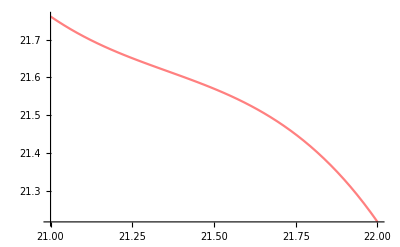

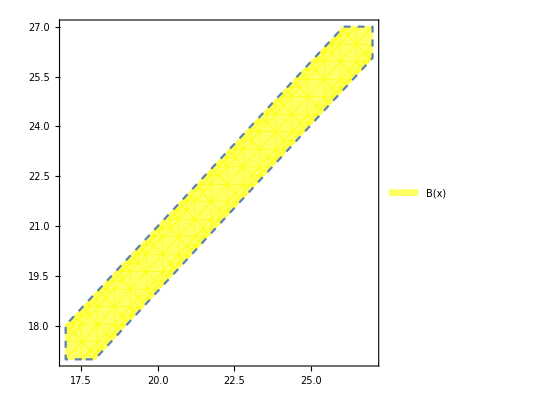

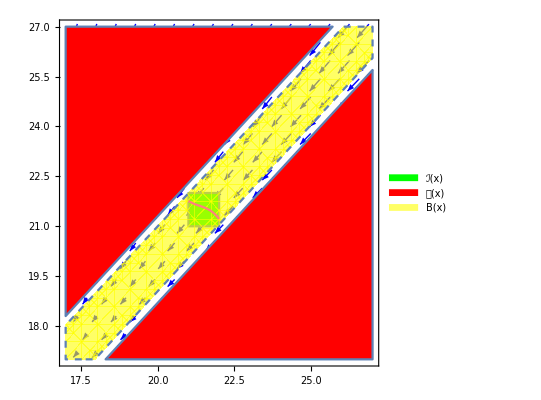

-Graphics-

```mathematica
(*phi=RegionPlot[(x≥0&&x≤0.7&&y≥0.7&&y≤1.5&&y-x<=0.8),{x,0,0.7},{y,0.7,1.5},PlotPoints->50,BoundaryStyle->Directive[RGBColor[0,0.5,0], Thin],PlotStyle->Directive[Blue]]
(*phi ->initial region *)
psi1=RegionPlot[(x≥0&&x≤8&&y≥0&&y≤8&&(y-x)*(y-x)>=1),{x,0,8},{y,0,8},PlotPoints->70,PlotStyle->Directive[Red],BoundaryStyle->Directive[RGBColor[0.5,0,0], Opacity[0.05],Thin]]*)
(* we first give ReLU fuction*)
relu[x_] =If[x>=0,x,0]
(*psi -> unsafe region*)

(*B(x,xˆ)=0.9227x1*x1+0.2348v1*v1+0.9227x2*x2+0.2348v2*v2+0.006x1*v1−0.006x2*v1−0.006x1*v2−0.006x2*v2−0.4696v1*v2−1.845x1x2−0.0002*x2+0.0728,*)
(* this B is only for test*)
(*bc=0.9227*x*x + 0.9227*y*y -1.845*x*y  - 0.0002*y + 0.0728*)
x1= 21.75
x2 = 21.25
bc = 0.0929392728715566*relu[-2.10982744905372*x1+1.16346513536268*x2+0.494264421524521*x+0.206951023831072*y+1.4016981895889]-0.235012516228133*relu[-1.64224927739583*x1+1.13196205562523*x2+0.746817806830182*x-1.44982799820047*y+1.57317625192024]+0.115393787356467*relu[-1.44418456383108*x1+1.67392663393435*x2+1.12620472724211*x-1.14689032949426*y-2.80796355658205]+0.694176251576024*relu[-1.30762800035759*x1-0.142154966451366*x2-0.780216766537476*x+0.510221069354175*y-1.57385145892744]+0.0684169941060288*relu[-0.801811485160055*x1+0.773105450982331*x2-2.54090993528104*x+2.53493942144905*y-0.42793049297048]-0.339343780108287*relu[-0.718396551065054*x1+0.0115239322904548*x2+0.0364859673088556*x+0.114060116128125*y+2.11729170269886]-0.0701767871989761*relu[-0.497163134116573*x1-1.76316159518039*x2-0.692518548050902*x+1.26927430461324*y+2.15258375053521]-1.02230709224933*relu[-0.420373339361121*x1-0.778241984379268*x2+0.586734284630441*x+0.0901207532798795*y-0.646437211863935]-1.83101501579804*relu[-0.392731309515138*x1-0.970932250039672*x2+0.755524909367982*x+0.208393873854481*y-3.20582143035995]+0.443943954572989*relu[-0.13319251031543*x1-2.2004527587138*x2+0.144686270706564*x-0.0623222604675656*y+1.07512323458035]-1.5172902733055*relu[0.46527394886498*x1-1.72059513016592*x2+0.300826549956277*x+0.26069571244951*y-1.66325174540339]+0.635839943915016*relu[0.584740020112811*x1+1.17201458226725*x2-1.7394418594822*x-0.852351418261507*y-1.45567422716851]+0.0921481675553216*relu[0.646584692691175*x1-0.694117742072642*x2+3.20762517887897*x-3.17668165950155*y-1.79882451735439]+0.0499586936576099*relu[0.964060926786194*x1+0.582942638896432*x2-0.671181874348742*x-1.26324662722077*y-0.200818916731169]+0.0880957687208529*relu[1.49698610252439*x1-1.45906322009525*x2-1.87847093861363*x+1.91838032415829*y-1.16281697916442]+0.0965089220797452*relu[1.67206330030568*x1-1.74069310802252*x2+0.121556074982392*x-0.115670360435541*y-0.215048392272142]+0.659359231423058


(* xuebai *)
initialPlot=RegionPlot[(x≥21&&x≤22&&y≥21&&y≤22&&(y-x)*(y-x)<=1),{x,21,22},{y,21,22},PlotStyle->Directive[Green],PlotLegends->SwatchLegend[{"ℐ(x)"}]];
unsafePlot=RegionPlot[(17≥0&&x≤27&&y≥17&&y≤27&&(y-x)*(y-x)>=1.3*1.3),{x,17,27},{y,17,27},PlotStyle->Directive[Red],PlotLegends->SwatchLegend[{"𝒰(x)"}]];
bcPlot=RegionPlot[(x≥17&&x≤27&&y≥17&&y≤27&&bc<=1),{x,17,27},{y,17,27},BoundaryStyle->{Dashed},PlotStyle->Directive[Opacity[.6],Yellow],PlotLegends->SwatchLegend[{"B(x)"}]];
u = Random[Real,{0,1}]
x5 = u
(* this is controller*)
uhat  = -0.620935423169534*relu[-2.02603158531233*x1+0.379428028009936*x2+0.660050764780629*x-0.453028807943377*y-0.837941609493382*x5-1.57906017709966]-0.00866691831625059*relu[-1.62108967713863*x1+0.224787044044804*x2+0.308536417962728*x+0.80036473957708*y-0.516743939859624*x5-0.240382886701265]+1.23069956910834*relu[-0.0744765096849151*x1+0.603761045654598*x2-1.33468247844306*x-2.15314529401565*y-0.398478563773158*x5+0.831042358463886]+0.167637044693848*relu[0.0280556234903131*x1-0.497765883235089*x2-1.26417538210644*x+1.12622907871613*y+0.0427267467167157*x5-0.857625058716202]-0.0345412219861198*relu[0.184266663782139*x1-0.296318481674781*x2+0.58405490168188*x-0.425505060793168*y-1.46875011086186*x5+1.5150398640813]-0.0342318552126935*relu[0.298248101867746*x1-0.863109109646777*x2-0.22398635806403*x+0.414856393034983*y-1.60016810010055*x5+0.806572432289073]+0.0261392418040802*relu[0.331342271088*x1+0.934867698459171*x2-2.46185749232059*x+0.663838792292221*y-0.843453716275201*x5+1.5811414980025]-0.0201696375505661*relu[0.51514551666102*x1+0.476259677654219*x2-0.592354760531534*x-0.654248803966765*y+0.660136545488238*x5-1.20685953517205]+0.613195102268546
(*para*)
alpha=0.05
Te=15
ah=0.0036
Th=55
ae=0.008
(*vector*)
(*(1-2*alpha-ae-ah*u)*x[:,2]+alpha*x[:,0]+ae*Te+ah*Th*u*)
(*(1-2*alpha-ae-ah*(ctrl_nn(controller_input))[:,0])*x[:,3]+alpha*x[:,1]+ae*Te+ah*Th*(ctrl_nn(controller_input))[:,0]*)
flowPlot=VectorPlot[{(1-2*alpha-ae-ah*u)*x+alpha*x1+ae*Te+ah*Th*u-x,(1-2*alpha-ae-ah*uhat)*y+alpha*x2+ae*Te+ah*Th*uhat-y},{x,17,27},{y,17,27},VectorScaling->Automatic,VectorSizes->Automatic,VectorColorFunction->None,VectorStyle->Blue];

(*traj*)
(*varset = {x,y};
initialBoundary = (y-x)*(y-x)-0.8
domainRange={21,22}; 
flowVec = {(1-2*alpha-ae-ah*u)*x+alpha*x1+ae*Te+ah*Th*u-x,(1-2*alpha-ae-ah*uhat)*y+alpha*x2+ae*Te+ah*Th*uhat-y};
initialSamples=RandomPoint[ImplicitRegion[initialBoundary≤0,varSet],20];
traj[x0_]:=NDSolve[Join[Thread[#'[t]&/@varSet==(flowVec/.Table[varSet[[i]]->varSet[[i]][t],{i,1,Length[varSet]}])],Thread[#[0]&/@varSet==x0]],varSet,{t,0,20},Method->"StiffnessSwitching"];
trajPlot=ParametricPlot[Evaluate[(#[t]&/@varSet)/.traj[#]&/@initialSamples],{t,0,20},RegionFunction->((domainRange[[1]]≤#1≤domainRange[[2]])&&(domainRange[[1]]≤#2≤domainRange[[2]])&),PlotStyle->Directive[Black,Thickness[Medium]]](*/.Line[x_]:>Arrow[x]*);*)
inpolt = Plot[{-0.7467*x*x*x + 47.84*x*x -1021.99 * x + 7301.3},{x,21,22},PlotStyle->Directive[Pink]]
g_b = Show[bcPlot]
print(g_b);

graphics=Show[flowPlot,initialPlot,unsafePlot,bcPlot, inpolt ]
Print[graphics];
```

```mathematica
0
```

0

```mathematica
|
```